# SIESTA

## Mark Cianciosa 11/3/2022

This plots out the results of the VMEC magnetic axis compared to the SIESTA magnetic axis for various values of beta.

## Result Directories

## Load Result Directories

Finds every directory with VMEC and SIESTA runs.

```mathematica
parentDirectory=SystemDialogInput["Directory"]
```

/Users/m4c/Research/MHD_MILE_STONE/VMEC_SIESTA_AXIS/

Get a sorted list of each directory in the parent. The first directory failed to converge in SIESTA to remove that one form this list.

```mathematica
sortedDirectories[parent_]:=Sort[FileNames["*_*.*",parent],ToExpression[Last[StringSplit[#1,"_"]]]<ToExpression[Last[StringSplit[#2,"_"]]]&][[2;;]];
```

## VMEC Results

## Load VMEC Data

From a given directory load a VMEC file. All the wout files have the same name.

### VMEC Quantities

Load physical quantities from the wout file in a directory.

```mathematica
loadVMECQuantity[directory_,name_]:=Normal[Import[FileNameJoin[{directory,"wout_simple.vmec.nc"}],{"Datasets",name}]];
```

Plasma beta.

```mathematica
betatotal=ParallelMap[loadVMECQuantity[#,"betatotal"]&,sortedDirectories[parentDirectory]];
```

#### Fourier Quanities

Fourier quantities need to be summed. For the magnetic axis u does not matter in VMEC. For an axisymmetric case v does not matter.

```mathematica
vmecAxisR[directory_]:=Module[{xm,xn,rmnc},
xm=loadVMECQuantity[directory,"xm"];
xn=loadVMECQuantity[directory,"xn"];
rmnc=loadVMECQuantity[directory,"rmnc"];
Total[rmnc[[1]]*Cos[xm*0-xn*0]]
];
vmecAxisZ[directory_]:=Module[{xm,xn,rmnc},
xm=loadVMECQuantity[directory,"xm"];
xn=loadVMECQuantity[directory,"xn"];
rmnc=loadVMECQuantity[directory,"zmns"];
Total[rmnc[[1]]*Sin[xm*0-xn*0]]
];
```

R and Z Positions.

```mathematica
vmecR=ParallelMap[vmecAxisR[#]&,sortedDirectories[parentDirectory]];
vmecZ=ParallelMap[vmecAxisZ[#]&,sortedDirectories[parentDirectory]];
```

### Plots

Plot out the radial and vertical potion as a function of β.

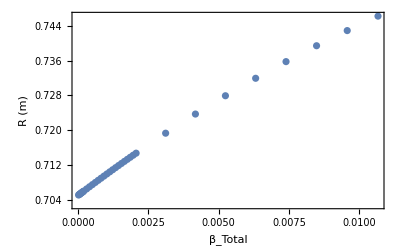

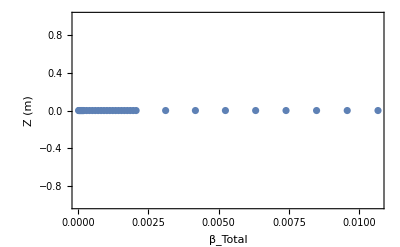

```mathematica
ListPlot[Transpose[{betatotal,vmecR}],Frame->True,FrameLabel->{{"R (m)",None},{"β_Total",None}},FrameStyle->Black]
ListPlot[Transpose[{betatotal,vmecZ}],Frame->True,FrameLabel->{{"Z (m)",None},{"β_Total",None}},FrameStyle->Black]
```

## Load SIESTA Data

From a given directory load a SIESTA restart file. All the restart files have the same name.

```mathematica
loadSIESTAQuantity[directory_,name_]:=Normal[Import[FileNameJoin[{directory,"siesta_restart_w7x.nc"}],{"Datasets",name}]];
```

### SIESTA Quantities

Load physical quantities from the restart file.

```mathematica
bsupsmns[directory_]:=loadSIESTAQuantity[directory,"JBsupssh_m_n_r_"];
bsupumnc[directory_]:=loadSIESTAQuantity[directory,"JBsupuch_m_n_r_"];
bsupvmnc[directory_]:=loadSIESTAQuantity[directory,"JBsupvch_m_n_r_"];
```

```mathematica
rmnc[directory_]:=loadSIESTAQuantity[directory,"rmnc_m_n_r_"];
zmns[directory_]:=loadSIESTAQuantity[directory,"zmns_m_n_r_"];
```

```mathematica
mpol[directory_]:=loadSIESTAQuantity[directory,"mpol"];
ntor[directory_]:=loadSIESTAQuantity[directory,"ntor"];
```

```mathematica
nrad[directory_]:=loadSIESTAQuantity[directory,"nrad"];
```

```mathematica
nfp[directory_]:=loadSIESTAQuantity[directory,"nfp"];
```

## Radial Interpolation

Interpolate the radial grids.

### Radial Grids

Radial grid for the full and half grid quantities.

```mathematica
sSIESTAF[directory_]:=Subdivide[0,1,nrad[directory]-1];
sSIESTAH[directory_]:=(sSIESTAF[directory][[;;-2]]+sSIESTAF[directory][[2;;]])/2;
```

### Interpolation Functions

Interpolate over entire positive to negative points to obtain the correct derivatives at the magnetic axis. Even m modes Fourier amplitudes will have the same parity. Odd modes Fourier amplitudes will have opposite parity.

#### SIESTA Functions

Half grid functions

```mathematica
bsupsmnsInt[directory_]:=Module[{halfGridS,mpolValue,ntorValue,bsupsmnsValue},
halfGridS=sSIESTAH[directory];
mpolValue=mpol[directory];
ntorValue=ntor[directory];
bsupsmnsValue=bsupsmns[directory];
Table[Interpolation[Join[Transpose[{Reverse[-halfGridS],Reverse[If[Mod[m,2]==0,1,-1]*bsupsmnsValue[[2;;,n+ntorValue+1,m+1]]]}],Transpose[{halfGridS,bsupsmnsValue[[2;;,n+ntorValue+1,m+1]]}]],InterpolationOrder->10],{n,-ntorValue,ntorValue,1},{m,0,mpolValue,1}]
];
bsupumncInt[directory_]:=Module[{halfGridS,mpolValue,ntorValue,bsupumncValue},
halfGridS=sSIESTAH[directory];
mpolValue=mpol[directory];
ntorValue=ntor[directory];
bsupumncValue=bsupumnc[directory];
Table[Interpolation[Join[Transpose[{Reverse[-halfGridS],Reverse[If[Mod[m,2]==0,1,-1]*bsupumncValue[[2;;,n+ntorValue+1,m+1]]]}],Transpose[{halfGridS,bsupumncValue[[2;;,n+ntorValue+1,m+1]]}]],InterpolationOrder->10],{n,-ntorValue,ntorValue,1},{m,0,mpolValue,1}]
];
bsupvmncInt[directory_]:=Module[{halfGridS,mpolValue,ntorValue,bsupvmncValue},
halfGridS=sSIESTAH[directory];
mpolValue=mpol[directory];
ntorValue=ntor[directory];
bsupvmncValue=bsupvmnc[directory];
Table[Interpolation[Join[Transpose[{Reverse[-halfGridS],Reverse[If[Mod[m,2]==0,1,-1]*bsupvmncValue[[2;;,n+ntorValue+1,m+1]]]}],Transpose[{halfGridS,bsupvmncValue[[2;;,n+ntorValue+1,m+1]]}]],InterpolationOrder->10],{n,-ntorValue,ntorValue,1},{m,0,mpolValue,1}]
];
```

Full grid functions

```mathematica
rmncInt[directory_]:=Module[{fullGridS,mpolValue,ntorValue,rmncValue},
fullGridS=sSIESTAF[directory];
mpolValue=mpol[directory];
ntorValue=ntor[directory];
rmncValue=rmnc[directory];
Table[Interpolation[Join[Transpose[{Reverse[-fullGridS[[2;;]]],Reverse[If[Mod[m,2]==0,1,-1]*rmncValue[[2;;,n+ntorValue+1,m+1]]]}],Transpose[{fullGridS,rmncValue[[;;,n+ntorValue+1,m+1]]}]],InterpolationOrder->10],{n,-ntorValue,ntorValue,1},{m,0,mpolValue,1}]
];
zmnsInt[directory_]:=Module[{fullGridS,mpolValue,ntorValue,zmnsValue},
fullGridS=sSIESTAF[directory];
mpolValue=mpol[directory];
ntorValue=ntor[directory];
zmnsValue=zmns[directory];Table[Interpolation[Join[Transpose[{Reverse[-fullGridS[[2;;]]],Reverse[If[Mod[m,2]==0,1,-1]*zmnsValue[[2;;,n+ntorValue+1,m+1]]]}],Transpose[{fullGridS,zmnsValue[[;;,n+ntorValue+1,m+1]]}]],InterpolationOrder->10],{n,-ntorValue,ntorValue,1},{m,0,mpolValue,1}]
];
```

## Inverse Fourier Transform

Transform Fourier representation to real space.

### SIESTA Transform

SIESTA Functions take the following form depending on the parity.

A(s,u,v)=∑_m ∑_n A_mnc(s)cos(m*u+nfp*n*v)

## Field Line Following

```mathematica
fieldLine[directory_][vend_]:=Module[{bsubsint,bsubuint,bsubvint,rint,zint,bsups,bsupu,bsupv,rsuv,zsuv,mpolValue,ntorValue,nfpValue,vendValue},
bsubsint=bsupsmnsInt[directory];
bsubuint=bsupumncInt[directory];
bsubvint=bsupvmncInt[directory];
rint=rmncInt[directory];
zint=zmnsInt[directory];
mpolValue=mpol[directory];
ntorValue=ntor[directory];
nfpValue=nfp[directory];
bsups[s_,u_,v_]:=Evaluate[Sum[bsubsint[[n+ntorValue+1,m+1]][s]*Sin[m*u+nfpValue*n*v],{m,0,mpolValue,1},{n,-ntorValue,ntorValue,1}]];
bsupu[s_,u_,v_]:=Evaluate[Sum[bsubuint[[n+ntorValue+1,m+1]][s]*Cos[m*u+nfpValue*n*v],{m,0,mpolValue,1},{n,-ntorValue,ntorValue,1}]];
bsupv[s_,u_,v_]:=Evaluate[Sum[bsubvint[[n+ntorValue+1,m+1]][s]*Cos[m*u+nfpValue*n*v],{m,0,mpolValue,1},{n,-ntorValue,ntorValue,1}]];
rsuv[s_,u_,v_]:=Evaluate[Sum[rint[[n+ntorValue+1,m+1]][s]*Cos[m*u+nfpValue*n*v],{m,0,mpolValue,1},{n,-ntorValue,ntorValue,1}]];
zsuv[s_,u_,v_]:=Evaluate[Sum[zint[[n+ntorValue+1,m+1]][s]*Sin[m*u+nfpValue*n*v],{m,0,mpolValue,1},{n,-ntorValue,ntorValue,1}]];
vendValue=vend/nfpValue;
Reap[
Sow[{{0.0,Mod[0.0,2Pi]},{rsuv[0.0,0.0,0.0],zsuv[0.0,0.0,0.0]}},a];
NDSolve[
{s'[v]==bsups[s[v],u[v],v]/bsupv[s[v],u[v],v],
u'[v]==bsupu[s[v],u[v],v]/bsupv[s[v],u[v],v],
s[0]==0.0,u[0]==0.0,
WhenEvent[Sin[v*nfpValue]==Sin[0.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},aa],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[9.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},bb],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[18.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},cc],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[27.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},dd],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[36.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ee],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[45.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ff],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[54.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},gg],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[63.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},hh],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[72.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ii],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[81.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},jj],Null]],
WhenEvent[Cos[v*nfpValue]==Cos[90.0*Pi/180.0],If[Sin[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},kk],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[99.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ll],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[108.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},mm],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[117.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},nn],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[126.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},oo],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[135.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},pp],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[144.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},qq],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[153.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},rr],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[162.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ss],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[171.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},tt],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[180.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},uu],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[189.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},vv],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[198.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ww],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[207.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},xx],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[216.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},yy],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[225.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},zz],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[234.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},aaa],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[245.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},bbb],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[252.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ccc],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[261.0*Pi/180.0],If[Cos[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ddd],Null]],
WhenEvent[Cos[v*nfpValue]==Cos[270.0*Pi/180.0],If[Sin[v*nfpValue]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},eee],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[279.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},fff],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[288.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ggg],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[297.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},hhh],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[306.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},iii],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[315.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},jjj],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[324.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},kkk],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[333.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},lll],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[342.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},mmm],Null]],
WhenEvent[Sin[v*nfpValue]==Sin[351.0*Pi/180.0],If[Cos[v*nfpValue]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},nnn],Null]]
},{s,u},{v,0.0,vendValue},Method->{"EquationSimplification"->"Residual"}
],{aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo,pp,qq,rr,ss,tt,uu,vv,ww,xx,yy,zz,aaa,bbb,ccc,ddd,eee,fff,ggg,hhh,iii,jjj,kkk,lll,mmm,nnn}
]];
```

Trace all the magnetic axis data.

```mathematica
data=ParallelMap[fieldLine[#][1000*2*Pi][[2,1,1,;;,2]]&,sortedDirectories[parentDirectory]];
```

Get the statistics.

```mathematica
aveSIESTAR=Map[Total[#[[;;,1]]]/Length[#[[;;,1]]]&,data];
aveSIESTAZ=Map[Total[#[[;;,2]]]/Length[#[[;;,2]]]&,data];
```

```mathematica
maxSIESTAR=Map[Max[#]&,data[[;;,;;,1]]];
maxSIESTAZ=Map[Max[#]&,data[[;;,;;,2]]];
```

```mathematica
minSIESTAR=Map[Min[#]&,data[[;;,;;,1]]];
minSIESTAZ=Map[Min[#]&,data[[;;,;;,2]]];
```

```mathematica
siestaErrorR=Table[{betatotal[[i]],Interval[{minSIESTAR[[i]],maxSIESTAR[[i]]}]},{i,Length[betatotal]}];
siestaErrorZ=Table[{betatotal[[i]],Interval[{minSIESTAZ[[i]],maxSIESTAZ[[i]]}]},{i,Length[betatotal]}];
```

## Plots

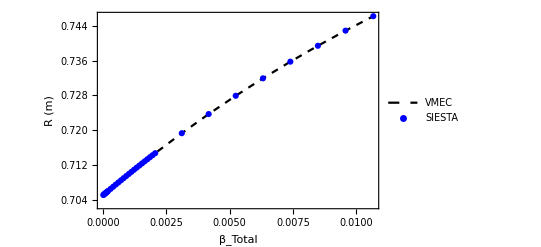

```mathematica
ListPlot[{Transpose[{betatotal,vmecR}],siestaErrorR},Frame->True,FrameStyle->Black,Joined->{True,False},FrameLabel->{{"R (m)",None},{"β_Total",None}},PlotStyle->{Directive[Black,Dashed],Blue},PlotLegends->{"VMEC","SIESTA"}]
```

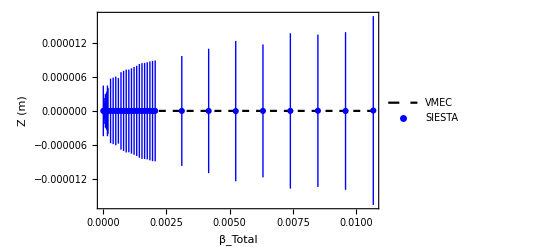

```mathematica
ListPlot[{Transpose[{betatotal,vmecZ}],siestaErrorZ},Frame->True,PlotRange->Full,FrameStyle->Black,FrameStyle->Black,Joined->{True,False},FrameLabel->{{"Z (m)",None},{"β_Total",None}},PlotStyle->{Directive[Black,Dashed],Blue},PlotLegends->{"VMEC","SIESTA"}]
```

```mathematica
siestaError2R=Table[{betatotal[[i]],Interval[{-Abs[minSIESTAR[[i]]-vmecR[[i]]],Abs[maxSIESTAR[[i]]-vmecR[[i]]]}]},{i,Length[betatotal]}];
siestaError2Z=Table[{betatotal[[i]],Interval[{-Abs[minSIESTAZ[[i]]-vmecZ[[i]]],Abs[maxSIESTAZ[[i]]-vmecZ[[i]]]}]},{i,Length[betatotal]}];
```

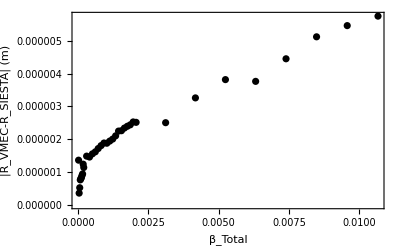

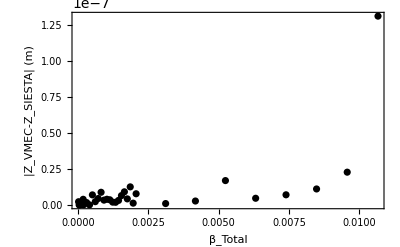

```mathematica
ListPlot[Transpose[{betatotal,Abs[vmecR-aveSIESTAR]}],Frame->True,FrameStyle->Black,FrameLabel->{{"|R_VMEC-R_SIESTA| (m)",None},{"β_Total",None}},PlotStyle->Black,PlotRange->Full]
ListPlot[Transpose[{betatotal,Abs[vmecZ-aveSIESTAZ]}],Frame->True,FrameStyle->Black,FrameLabel->{{"|Z_VMEC-Z_SIESTA| (m)",None},{"β_Total",None}},PlotStyle->Black,PlotRange->Full]
```

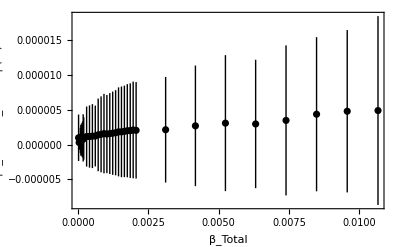

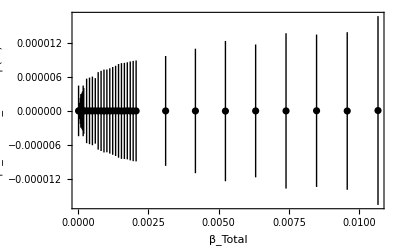

```mathematica
ListPlot[siestaError2R,Frame->True,FrameStyle->Black,FrameLabel->{{"|R_VMEC-R_SIESTA| (m)",None},{"β_Total",None}},PlotStyle->Black,PlotRange->Full]
ListPlot[siestaError2Z,Frame->True,FrameStyle->Black,FrameLabel->{{"|Z_VMEC-Z_SIESTA| (m)",None},{"β_Total",None}},PlotStyle->Black,PlotRange->Full]
```